```mathematica
A DsixTools Program
This notebook shows how to run a loop with varying WCs at the high scale and obtain results at the EW scale.
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Start DsixTools

```mathematica
Needs["DsixTools`"]
```

DsixTools 1.0

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.XXXXX

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

## Read input files

```mathematica
ReadInputFiles["Options.dat","WCsInput.dat","SMInput.dat"];
```

Input: SMEFT Wilson coefficients

## Load SMEFTrunner module

```mathematica
LoadModule["SMEFTrunner"]
```

SMEFTrunner

DsixTools module for the RGE running of the Standard Model Effective Theory

## Loops using the SMEFTrunner module

```mathematica
(* Load SMEFT β functions *)
LoadBetaFunctions;
```

Loading SMEFT β functions

```mathematica
(* Number of points *)
nPoints=20;
```

```mathematica
(* Loop 1: Subscript[(Subscript[C, lq]^(1)), 2223](Subscript[μ, EW]) as a function of Subscript[(Subscript[C, φq]^(1)), 23](Λ) *)
MinφQ1=-1;
MaxφQ1=1;
xLoop1={};
yLoop1={};

Do[

φQ1Value=MinφQ1+(i-1)(MaxφQ1-MinφQ1)/(nPoints-1)//N;
NewInput[φQ1[2,3],φQ1Value,input];

Print["(C_φq^(1))_23(Λ) = ",φQ1Value, " , ",i/nPoints*100.0,"%"];

RunRGEsSMEFT;

AppendTo[xLoop1,φQ1Value];
AppendTo[yLoop1,outSMEFTrunner[[310]]/.t->tLOW];

,{i,1,nPoints}];
```

(C_φq^(1))_23(Λ) = -1. , 5.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.894737 , 10.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.789474 , 15.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.684211 , 20.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.578947 , 25.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.473684 , 30.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.368421 , 35.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.263158 , 40.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.157895 , 45.%

Running

Running finished!

(C_φq^(1))_23(Λ) = -0.0526316 , 50.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.0526316 , 55.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.157895 , 60.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.263158 , 65.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.368421 , 70.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.473684 , 75.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.578947 , 80.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.684211 , 85.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.789474 , 90.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 0.894737 , 95.%

Running

Running finished!

(C_φq^(1))_23(Λ) = 1. , 100.%

Running

Running finished!

```mathematica
(* We restore the original input *)
NewInput[φQ1[2,3],0,input];
```

```mathematica
(* Loop 2: Subscript[(Subscript[C, dφ]), 33](Subscript[μ, EW]) as a function of Subscript[μ, EW] *)
MinμEW=50;
MaxμEW=150;
xLoop2={};
yLoop2={};

Do[

μEWValue=MinμEW+(i-1)(MaxμEW-MinμEW)/(nPoints-1)//N;
NewScale["low",μEWValue];

Print["μ_EW = ",μEWValue, " GeV , ",i/nPoints*100.0,"%"];

RunRGEsSMEFT;

AppendTo[xLoop2,μEWValue];
AppendTo[yLoop2,outSMEFTrunner[[68]]/.t->tLOW];

,{i,1,nPoints}];
```

μ_EW = 50. GeV , 5.%

Running

Running finished!

μ_EW = 55.2632 GeV , 10.%

Running

Running finished!

μ_EW = 60.5263 GeV , 15.%

Running

Running finished!

μ_EW = 65.7895 GeV , 20.%

Running

Running finished!

μ_EW = 71.0526 GeV , 25.%

Running

Running finished!

μ_EW = 76.3158 GeV , 30.%

Running

Running finished!

μ_EW = 81.5789 GeV , 35.%

Running

Running finished!

μ_EW = 86.8421 GeV , 40.%

Running

Running finished!

μ_EW = 92.1053 GeV , 45.%

Running

Running finished!

μ_EW = 97.3684 GeV , 50.%

Running

Running finished!

μ_EW = 102.632 GeV , 55.%

Running

Running finished!

μ_EW = 107.895 GeV , 60.%

Running

Running finished!

μ_EW = 113.158 GeV , 65.%

Running

Running finished!

μ_EW = 118.421 GeV , 70.%

Running

Running finished!

μ_EW = 123.684 GeV , 75.%

Running

Running finished!

μ_EW = 128.947 GeV , 80.%

Running

Running finished!

μ_EW = 134.211 GeV , 85.%

Running

Running finished!

μ_EW = 139.474 GeV , 90.%

Running

Running finished!

μ_EW = 144.737 GeV , 95.%

Running

Running finished!

μ_EW = 150. GeV , 100.%

Running

Running finished!

## Results

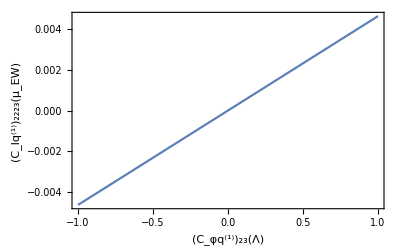

```mathematica
plot1=ListPlot[Transpose[{xLoop1,yLoop1}],Joined->True,Frame->True,Axes->False,PlotRange->{{MinφQ1,MaxφQ1},Automatic},FrameLabel->{"(C_φq^(1))_23(Λ)","(C_lq^(1))_2223(μ_EW)",None,None}]
```

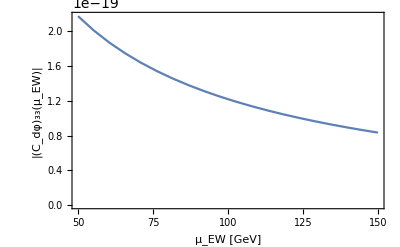

```mathematica
plot2=ListPlot[Transpose[{xLoop2,Abs[yLoop2]}],Joined->True,Frame->True,Axes->False,PlotRange->{{MinμEW,MaxμEW},Automatic},FrameLabel->{"μ_EW [GeV]","|(C_dφ)_33(μ_EW)|",None,None}]
```